# Exercise 10

As with all of the exercises you will complete in this course, you will be expected to turn your *.nb file in to the course TA before the next lecture.  Please do so by e-mailing your completed exercise file to Lan Yu (ece329.uiuc@gmail.com), make sure you name the file using the following notation: “Exn_Last_First.nb”, where n is the Exercise number (in this case, 10), and First and Last would be your first and last name.  So my submission to Lan for this exercise would be titled “Ex10_Wasserman_Dan.nb”.  You will receive full credit for your exercise if it turned in before the next lecture (Lecture n+1).  No late submissions will be accepted.

## Objective/Overview:

In today’s exercise, we are going to continue developing an understanding of capacitance.  In particular, we will focus on the capacitance of a pn-junction diode.

```mathematica
ClearAll[eslab1,eslab2,etotal,vpn,qpn,cappn1]
```

## pn-junctions

In class we already determined the capacitance of two commonly used systems: the parallel plate capacitor and the coax cable.  Both of these geometries are of fundamental importance for electromagnetic applictions, as they are standard geometries from which we make transmission lines (a subject we will spend some time on in coming weeks).  pn-junction diodes, on the other hand, are more important for electronic applications, and the capacitance of these structures is typically leveraged for electronics and not for E&M applications (though this is not always the case).  Let’s review what we know about pn-junctions first:
We can model the pn junction as two slabs of uniform charge density, where the total charge in each of the slabs is equal in magnitude and opposite in sign.  In the class notes, we treat these slabs as basically just a bunch of floating charge (ϵ=ϵ_o), but in real life, they consist of ionized dopants in a semiconductor material, and therefore will have a permittivity greater than that of vaccuum (ϵ=ϵ_r ϵ_o).  We wil take the simplified approach, ϵ=ϵ_o.
In order to determine the capacitance of any structure, what we are looking for is the relationship between voltage and charge.  In this case, it is the voltage drop across the pn-junction (something we have already found) and the charge (ionized dopants).
We can find the potential by either using Gauss’s Law to find the electric field from each slab, and then take the line integral to find the voltage drop, or we can use Poisson’s Equation to find the potential directly from the charge distribution. Let’s use Gauss’s Law.  Remember, w_1 ρ_1=w_2 ρ_2.

```mathematica
eps0=8.85*10^-12;k=1/(4*Pi*eps0);
```

```mathematica
eslab1[w1_,rho1_]:=Piecewise[{{-rho1*w1/(2*eps0),z<-w1},{rho1*(z+w1/2)/eps0,-w1≤ z≤0},{rho1*w1/(2*eps0),z>0}}]
```

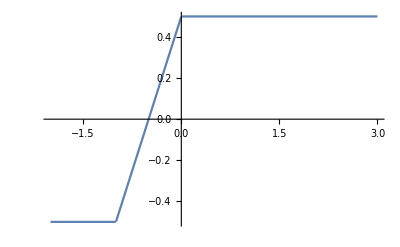

```mathematica
Plot[eslab1[1,eps0],{z,-2,3}]
```

```mathematica
eslab2[w2_,rho2_]:=Piecewise[{{-rho2*w2/(2*eps0),z<0},{rho2*(z-w2/2)/eps0,0≤ z≤w2},{rho2*w2/(2*eps0),z>w2}}]
```

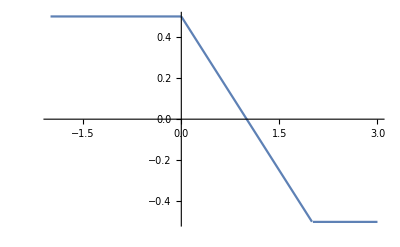

```mathematica
Plot[eslab2[2,-eps0/2],{z,-2,3}]
```

Note that in inputting the values for w_2 and ρ_2, I made sure that w_1 ρ_1=w_2 ρ_2.  The combined field is then:

```mathematica
etotal[w1_,rho1_,w2_,rho2_]:=eslab1[w1,rho1]+eslab2[w2,rho2]
```

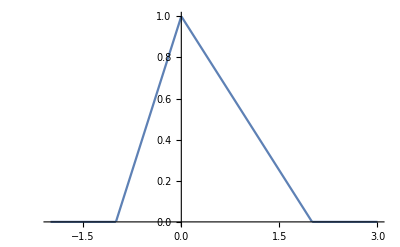

```mathematica
Plot[etotal[1,eps0,2,-eps0/2],{z,-2,3}]
```

We can find the potential across the junction, from -w1 to w2, by taking the line integral

```mathematica
vpn[w1_,rho1_,w2_,rho2_]:=Integrate[-etotal[w1,rho1,w2,rho2],{z,-w1,w2}]
```

```mathematica
vpn[1,eps0,2,-eps0/2]
```

-1.5

So we can find the potential for a given configuration of charge.  However, in the real world, we typically apply a voltage across the junction, which then determines w1 and w2.  If we can figure out the relationship between Voltage and w1,w2, for a given ρ_1 and ρ_2, then we should be able to find the capacitance of the junction.

## Junction Capacitance

We can see from the above, or from previous lectures and exercises, that our Voltage is nothing more than the integral of the electric field across our junction, or graphically, the area of the plot above.  Let’s do a little quick algebra:
V=w_1/2(ρ_1 w_1)/ϵ_o+w_2/2(ρ_1 w_1)/ϵ_o=(ρ_1 w_1)/(2 ϵ_o)(w_1+w_2)=(ρ_2 w_2)/(2 ϵ_o)(w_1+w_2)
w_1=(2 ϵ_o V)/(ρ_1(w_1+w_2)) , w_2=(2 ϵ_o V)/(ρ_2(w_1+w_2))
w_1+w_2=(2 ϵ_o V)/(ρ_1(w_1+w_2))(1/ρ_1+1/ρ_2) 
w_1+w_2=√(2 ϵ_o V((ρ_1+ρ_2)/(ρ_1 ρ_2)))
We can see now that the junction width depends on V, but this is not a linear dependence!!  So we cannot use Q=CV, to determine our capacitance.  Instead, we will need to use the more general definition of capacitance: C=dQ/dV...in other words, the capacitance is defined as the change in charge for a differential change in V, at a given V!
What is our charge Q?  Well, if we think about the junction as a parallel plate capacitor, we have two “plates” of charge, which are our slabs.  So the charge on the plates are Q=wρA, where A is the area of our pn-junction.
Q=ρ_1w_1 A=(2 ϵ_o VA)/(w_1+w_2)=(2 ϵ_o VA)/(√(2 ϵ_o V((ρ_1+ρ_2)/(ρ_1 ρ_2))))=A√(2 ϵ_o V((ρ_1 ρ_2)/(ρ_1+ρ_2)))
Below, write a function for Q (with rho1, rho2, and area as inputs), and plot Q as a function of voltage (v)  (for rho1=eps0, rho2=eps0, and area=1E-4). .

```mathematica
qpn[rho1_,rho2_,area_]:=area*Sqrt[2*eps0*v*(rho1*rho2/(rho1+rho2))]
```

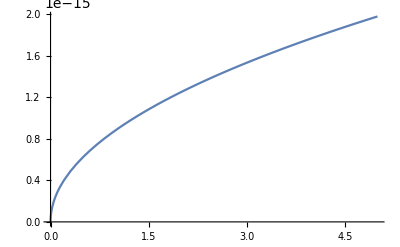

```mathematica
Plot[qpn[eps0,eps0,1*10^-4],{v,0,5}]
```

Now, calculate the capacitance of the above pn-junction, and plot the capacitance of the junction for the same parameters as above

```mathematica
cappn1=D[qpn[eps0,eps0,1*10^-4],v]
```

(4.425×10^-16)/(√v)

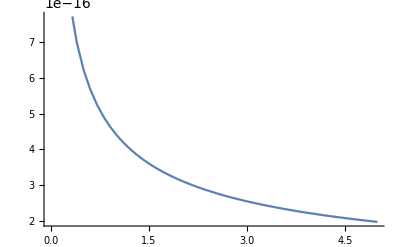

```mathematica
Plot[cappn1,{v,0,5}]
```

## Our First Interactive Plots

One of the powerful tools available in Mathematica is the Computable Document Format (CDF).  The CDF is an interactive document that allows users to manipulate plots and expressions in real time.  We will start using CDFs a lot during this course, but for today, we are just going to make our first interactive plots, a basic starting point for 
As an example, let’s do a very simple Manipulate plot.  We will look at a plot of the sum of two sin waves of different frequencies.

```mathematica
Manipulate[Plot[Sin[a*x]+Sin[b*x],{x,0,50}],{a,3,5},{b,3,5}]
```

OK.  Now that you get the basic idea, create a plot that gives capacitance vs. voltage of a pn-junction as a function of rho1, rho2, and area.  In a typical pn junction, you typically describe the doping concentration (not the charge density), of course to convert from doping concentration to charge density, you just multiply the doping concetration by the charge of a proton: 1.6E-19C.  Below I give the typical ranges for the inputs:

rho1,rho2-->doping densities typically run from 1E21 to 1E24 dopants/m^3, so your rho’s should go from 1.6E2 to 1.6E5 C/m^3.  We can do discrete choices for inputs by replacing the range {rho1, 1.6E2,1.6E5} by {rho1,{1.6E2, 1.6E3, 1.6E4...}}.

area-->the area of a pn junction could be anything from 1um x 1um to 1mmx1mm, but let’s give choice of discrete areas: 1E-10, 1E-9, 1E-8...1E-6 m^2.  We can do discrete choices for inputs by replacing the range {area, 1E-10,1E-6} by {area,{1E-10, 1E-9, 1E-8...}}.

Finally, because we are in a semiconductor, you should replace ϵ_o with ϵ_rϵ_o.  A typical semiconductor has ϵ_r=12, so you can use this for your interactive plot.

```mathematica
Manipulate[Plot[area*Sqrt[(12*eps0/(2*v))*(rho1*rho2/(rho1+rho2))],{v,0,5}],{rho1,{160,1600,16000,160000}},{rho2,{160,1600,16000,160000}},{area,{10^-10,10^-9,10^-8,10^-7,10^-6}}]
```